```mathematica
chi2mod[N0_,NBSM]
frac=N0/NBSM;
 2*(NBSM-N0+N0*Log[frac])
```

```mathematica
Limit[2(NBSM-N0+N0*Log[N0/NBSM]),NBSM->0]
```

N0 ∞

```mathematica
Asymptotic[2(NBSM-N0+N0*Log[N0/NBSM]),NBSM->0]
```

2 N0 log(N0/NBSM)

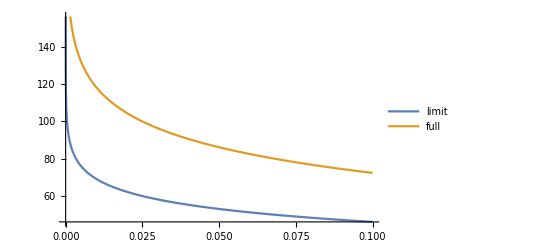

```mathematica
Plot[{10 Log[10/NBSM],2(NBSM-10+10*Log[10/NBSM])},{NBSM,0,0.1},PlotLegends->{"limit","full"}]
```

```mathematica
Ham={{0,0,0},{0,dm21/(2En),0},{0,0,dm31/(2En)}}
```

(0 | 0 | 0
0 | dm21/(2 En) | 0
0 | 0 | dm31/(2 En))

```mathematica
theta12=ArcSin[Sqrt[0.303]];
theta13=ArcSin[Sqrt[0.02225]];
theta23=ArcSin[Sqrt[0.572]];
s12=Sin[theta12];c12=Cos[theta12];
s13=Sin[theta13];c13=Cos[theta13];
s23=Sin[theta23];c23=Cos[theta23];

U[δ_]:={{c12 c13,s12 c13,s13 Exp[-I δ]},{-s12 c23-c12 s23 s13 Exp[I δ],c12 c23-s12 s23 s13 Exp[I δ],s23 c13},{s12 s23-c12 c23 s13 Exp[I δ],-c12 s23-s12 c23 s13 Exp[I δ],c23 c13}};

MatrixForm[U[0]]
U[0].{1,0,0}
{1,0,0}.U[0]
```

(0.825525 | 0.544296 | 0.149164
-0.454301 | 0.484084 | 0.747846
0.334841 | -0.685131 | 0.646898)

{0.825525,-0.454301,0.334841}

{0.825525,0.544296,0.149164}

```mathematica
[[-0.83+0.j-0.54+0.j-0.15+0.j][0.45+0.j-0.48+0.j-0.75+0.j][-0.33+0.j 0.69+0.j-0.65+0.j]]
```

```mathematica
{vals,vecs}=Eigensystem[mat];
ord=Ordering[vals];
valsSorted=vals[[ord]];
vecsSorted=vecs[[ord]];
mat
vecsSorted
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 2)

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

```mathematica
params={aee,aem,aet,amm,amt,att};

Do[
params2=DeleteCases[params,p];
mat={{aee,aem,aet},{aem,amm,amt},{aet,amt,att}}/. Thread[params2->0]/. p->2;
Print["Nonzero: ",p];
{vals,vecs}=Eigensystem[mat];
ord=Ordering[vals];
valsSorted=vals[[ord]];
vecsSorted=vecs[[ord]];
Print[mat,Transpose[vecsSorted],vecsSorted.mat.Transpose[vecsSorted]];
Print[valsSorted];
Print["---"];,{p,params}]
```

Nonzero: aee

(2 | 0 | 0
0 | 0 | 0
0 | 0 | 0)(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)(0 | 0 | 0
0 | 0 | 0
0 | 0 | 2)

{0,0,2}

---

Nonzero: aem

(0 | 2 | 0
2 | 0 | 0
0 | 0 | 0)(-1 | 0 | 1
1 | 0 | 1
0 | 1 | 0)(-4 | 0 | 0
0 | 0 | 0
0 | 0 | 4)

{-2,0,2}

---

Nonzero: aet

(0 | 0 | 2
0 | 0 | 0
2 | 0 | 0)(-1 | 0 | 1
0 | 1 | 0
1 | 0 | 1)(-4 | 0 | 0
0 | 0 | 0
0 | 0 | 4)

{-2,0,2}

---

Nonzero: amm

(0 | 0 | 0
0 | 2 | 0
0 | 0 | 0)(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)(0 | 0 | 0
0 | 0 | 0
0 | 0 | 2)

{0,0,2}

---

Nonzero: amt

(0 | 0 | 0
0 | 0 | 2
0 | 2 | 0)(0 | 1 | 0
-1 | 0 | 1
1 | 0 | 1)(-4 | 0 | 0
0 | 0 | 0
0 | 0 | 4)

{-2,0,2}

---

Nonzero: att

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 2)(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)(0 | 0 | 0
0 | 0 | 0
0 | 0 | 2)

{0,0,2}

---

```mathematica
Ham
```

(0 | 0 | 0
0 | dm21/(2 En) | 0
0 | 0 | dm31/(2 En))

```mathematica
mat=U[0].Ham.ConjugateTranspose[U[0]]+En^(d-3){{aee,aem,aet},{aem,amm,amt},{aet,amt,att}}/.{dm21->7.5*10^-5*10^-18,dm31->2.5*10^-3*10^-18,En->1 10^9(*in GeV*),d->6}/.{aee->0,aem->0,aet->0,ame->0,amm->0,amt->10^-46,att->0}

{vals,vecs}=Eigensystem[mat];
ord=Ordering[vals];          (*indices that sort eigenvalues ascending*)
valsSorted=vals[[ord]];
U[0]
pmns=Transpose[vecs[[ord]]]
ConjugateTranspose[pmns].mat.pmns;
probavg[a_,b_]:=Sum[Abs[pmns[[a,i]]]^2 Abs[pmns[[b,i]]]^2,{i,1,3}]
matprob=Table[probavg[i,j],{i,1,3},{j,1,3}];
```

(3.89222×10^-32 | 1.49321×10^-31 | 1.06633×10^-31
1.49321×10^-31 | 7.07879×10^-31 | 1.×10^-19
1.06633×10^-31 | 1.×10^-19 | 5.40699×10^-31)

(0.825525 | 0.544296 | 0.149164
-0.454301 | 0.484084 | 0.747846
0.334841 | -0.685131 | 0.646898)

(3.01844×10^-13 | -1. | 1.80991×10^-12
-0.707107 | 1.06632×10^-12 | 0.707107
0.707107 | 1.49319×10^-12 | 0.707107)

```mathematica
U[0]
```

(0.825525 | 0.544296 | 0.149164
-0.454301 | 0.484084 | 0.747846
0.334841 | -0.685131 | 0.646898)

```mathematica
U[0][[1]]
{0.82552514+0.j ,0.54429611+0.j ,0.14916434+0.j}
```

{0.825525,0.544296,0.149164}

{0.825525,0.544296,0.149164}

```mathematica
testprobavgEn[a_,b_,En_]:=Module[{mat,freeterm,Hamfunc,dm21,dm31,d,pmns,aee,amm,att,aem,aet,amt,vals,vecs,ord},
Hamfunc[dm21_,dm31_]:={{0,0,0},{0,dm21/(2En),0},{0,0,dm31/(2En)}};
freeterm=U[0].Hamfunc[dm21,dm31].ConjugateTranspose[U[0]]/.{dm21->7.5*10^-5*10^-18,dm31->2.5*10^-3*10^-18};mat=freeterm+ReplaceAll[-En^(d-3){{aee,aem,aet},{aem,amm,amt},{aet,amt,att}},{dm21->7.5*10^-5*10^-18,dm31->2.5*10^-3*10^-18(*,En->2.6 10^7*)(*in GeV*),d->4,aee->0,aem->0,aet->0,amm->0,amt->10^-36,att->0}];
{vals,vecs}=Eigensystem[mat];
ord=Ordering[vals];          (*indices that sort eigenvalues ascending*)
valsSorted=vals[[ord]];
pmns=Transpose[vecs[[ord]]];

Print[freeterm];
Print[mat-freeterm];
Print[valsSorted];
Print[Round[pmns,0.01]];
(*Print[ConjugateTranspose[pmns].mat.pmns];*)
Sum[Abs[pmns[[a,i]]]^2 Abs[pmns[[b,i]]]^2,{i,1,3}]]

(*1/3 testprobavgEn[1,3,2.5372062*10^7]+2/3 testprobavgEn[2,3,2.5372062*10^7]*)
testprobavgEn[2,2,2.5372062*10^7]
```

(1.53406×10^-30 | 5.88524×10^-30 | 4.20279×10^-30
5.88524×10^-30 | 2.78999×10^-29 | 2.33441×10^-29
4.20279×10^-30 | 2.33441×10^-29 | 2.13108×10^-29)

(0. | 0. | 0.
0. | 0. | -2.53721×10^-29
0. | -2.53721×10^-29 | 0.)

{-6.57147×10^-31,2.208×10^-29,2.93219×10^-29}

(0.96 | -0.23 | -0.18
-0.21 | -0.11 | -0.97
-0.2 | -0.97 | 0.15)

0.893269

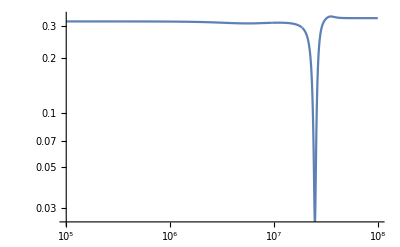

```mathematica
probavgEn[a_,b_,En_]:=Module[{mat,freeterm,Hamfunc,dm21,dm31,d,pmns,aee,amm,att,aem,aet,amt},
Hamfunc[dm21_,dm31_]:={{0,0,0},{0,dm21/(2En),0},{0,0,dm31/(2En)}};
freeterm=U[0].Hamfunc[dm21,dm31].ConjugateTranspose[U[0]]/.{dm21->7.5*10^-5*10^-18,dm31->2.5*10^-3*10^-18};mat=freeterm+ReplaceAll[-En^(d-3){{aee,aem,aet},{aem,amm,amt},{aet,amt,att}},{dm21->7.5*10^-5*10^-18,dm31->2.5*10^-3*10^-18(*,En->2.6 10^7*)(*in GeV*),d->4,aee->0,aem->0,aet->0,amm->0,amt->10^-36,att->0}];
{vals,vecs}=Eigensystem[mat];
ord=Ordering[vals];          (*indices that sort eigenvalues ascending*)
valsSorted=vals[[ord]];
pmns=Transpose[vecs[[ord]]];

(*Print[ConjugateTranspose[pmns].mat.pmns];*)
Sum[Abs[pmns[[a,i]]]^2 Abs[pmns[[b,i]]]^2,{i,1,3}]]

outflavor=3;
Plot[1/3 probavgEn[1,outflavor,En]+2/3 probavgEn[2,outflavor,En],{En,10^5,10^8},ScalingFunctions->{"Log","Log"},PlotRange->All]
```

choice of order of PMNS in free term matters

after resolving python issue, if peak survives, do it analytically ...

## analytic 2 flavors

### set up mixing matrix

```mathematica
Clear[mix2,free2,free2v2,mat2,vals,vecs]
mix2={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};free2={{0,0},{0,dm21/(2En)}};
free2v2=mix2.free2.Transpose[mix2];
mat2=free2v2+ReplaceAll[+(-1)^(d+1)En^(d-3){{aee,aem},{aem,amm}},{(*d->5,*)(*aee->0,aem->x ,amm->0*)}];
{vals,vecs}=Eigensystem[mat2];
(*normvecs={};*)
normvecs=Normalize/@vecs;
ord=Ordering[vals];          
mix2new=Transpose[normvecs[[ord]]];
mix2new=Simplify[mix2new,Assumptions->{dm21^2>0,dm21>0,x>0,θ>0,En>0}];
```

### offdiag vanishing case

```mathematica
mix12=ReplaceAll[mix2new[[1,2]],{aem->0 ,amm->0}];
Simplify[Solve[Numerator[mix12]==0,aee],d∈Integers]

mix12=ReplaceAll[mix2new[[1,2]],{aee->0 ,amm->0}];
repsolaem=Simplify[Solve[mix12==0,aem],d∈Integers]

Solve[x==aem/.repsolaem/.{dm21->2.521*10^-3*10^-18,θ->43.27 Degree,d->6,x->10^-55},En,Assumptions->En>0]
(*$\Delta m^2=2.521\times 10^{-3}\,\rm eV^2$,$\theta=\theta_{23}=43.27\degree*)
mix12=ReplaceAll[mix2new[[1,2]],{aee->0 ,aem->0}];
Simplify[Solve[Numerator[mix12]==0,amm],d∈Integers]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Simplify::infd: Expression (dm21 En^2 sin(2 θ) tan(2 θ))/(4 ((-En)^d-(-1)^d En^d)) simplified to ComplexInfinity.

{{aee→ComplexInfinity}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{aem→1/4 (-1)^d dm21 En^(2-d) sin(2 θ)},{aem→1/4 (-1)^d dm21 En^(2-d) sin(2 θ)}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{En→2.81631×10^8}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Simplify::infd: Expression -(dm21 En^2 sin(2 θ) tan(2 θ))/(4 ((-En)^d-(-1)^d En^d)) simplified to ComplexInfinity.

{{amm→ComplexInfinity}}

```mathematica
repsolaem//StandardForm
```

{{aem→1/4 (-1)^d dm21 En^(2-d) Sin[2 θ]},{aem→1/4 (-1)^d dm21 En^(2-d) Sin[2 θ]}}

```mathematica
Solve[aem==1/4 (-1)^d dm21 En^(2-d) Sin[2 θ],En]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{En→4^(1/(2-d)) ((aem (-1)^-d csc(2 θ))/dm21)^(1/(2-d))}}

```mathematica
En/.Solve[aem==1/4 (-1)^d dm21 En^(2-d) Sin[2 θ],En]/.{d->6,θ->43.27 Degree, dm21->2.521*10^-3*10^-18,aem->10^-55}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{2.81631×10^8}

### diag vanishing case

```mathematica
mix12=ReplaceAll[mix2new[[1,1]],{aem->0 ,amm->0}];
Simplify[Solve[Numerator[mix12]==0,aee],d∈Integers]

mix12=ReplaceAll[mix2new[[1,1]],{aee->0 ,amm->0}];
Simplify[Solve[Numerator[mix12]==0,aem],d∈Integers]
Simplify[Denominator[mix12]/.{Simplify[Solve[Numerator[mix12]==0,aem],d∈Integers]}/.(En^d-(-1)^d (-En)^d)->0]

mix12=ReplaceAll[mix2new[[1,1]],{aee->0 ,aem->0}];
Simplify[Solve[Numerator[mix12]==0,amm],d∈Integers]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{aee→ComplexInfinity}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{aem→1/4 (-1)^d dm21 En^(2-d) sin(2 θ)},{aem→1/4 (-1)^d dm21 En^(2-d) sin(2 θ)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(-dm21 En^(2-d) (En^d-(-1)^d (-En)^d) sin(2 θ) √(Abs[(En^(d-2) (dm21 cot(2 θ) En^2+csc(2 θ) √(dm21^2 En^4 ((-1)^(2 d) ((-En)^(2 d)-2 En^(2 d)) sin^2(2 θ) En^(-2 d)+1))))/(dm21 ((-1)^d (-En)^d-En^d))]^2+1) | -dm21 En^(2-d) (En^d-(-1)^d (-En)^d) sin(2 θ) √(Abs[(En^(d-2) (dm21 cot(2 θ) En^2+csc(2 θ) √(dm21^2 En^4 ((-1)^(2 d) ((-En)^(2 d)-2 En^(2 d)) sin^2(2 θ) En^(-2 d)+1))))/(dm21 ((-1)^d (-En)^d-En^d))]^2+1))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{amm→ComplexInfinity}}

## estimate

```mathematica
E^(d-3)a=dmsq/(2En)
```

```mathematica
a~E^(1-d)dmsq
```

```mathematica
Table[{d,Log10[En^(2-d)dmsq]},{d,3,8,1}]/.{En->10^5,dmsq->10^-21}//N//StandardForm
```

{{3.,-26.},{4.,-31.},{5.,-36.},{6.,-41.},{7.,-46.},{8.,-51.}}

```mathematica
Table[{d,Log10[En^(2-d)dmsq]},{d,3,8,1}]/.{En-> 10^10,dmsq->10^-21}//N//StandardForm
```

{{3.,-31.},{4.,-41.},{5.,-51.},{6.,-61.},{7.,-71.},{8.,-81.}}

```mathematica
Table[{d,Log10[En^(2-d)dmsq]},{d,3,8,1}]/.{En-> 10^9,dmsq->10^-21}//N//StandardForm
```

{{3.,-30.},{4.,-39.},{5.,-48.},{6.,-57.},{7.,-66.},{8.,-75.}}

```mathematica
Table[{20+10(d-3),-Log10[En^(2-d)dmsq]/.{En-> 10^9,dmsq->10^-21},(20+10(d-3)+40+10(d-3))/2,40+10(d-3)},{d,3,8,1}]//N
```

(20. | 30. | 30. | 40.
30. | 39. | 40. | 50.
40. | 48. | 50. | 60.
50. | 57. | 60. | 70.
60. | 66. | 70. | 80.
70. | 75. | 80. | 90.)

```mathematica
Table[{En,Log10[En^(2-d)dmsq]}/.{d->5,En-> 10^x,dmsq->10^-21},{x,5,11}]//N//StandardForm
```

{{100000.,-36.},{1.×10^6,-39.},{1.×10^7,-42.},{1.×10^8,-45.},{1.×10^9,-48.},{1.×10^10,-51.},{1.×10^11,-54.}}

```mathematica
Clear[mix2,free2,free2v2,mat2,vals,vecs]
mix2={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};free2={{0,0},{0,dm21/(2En)}};
free2v2=mix2.free2.Transpose[mix2];
mat2=free2v2+ReplaceAll[+(-1)^(d+1)En^(d-3){{aee,aem},{aem,amm}},{d->5,aee->0,aem->x ,amm->0}];
{vals,vecs}=Eigensystem[mat2];
(*normvecs={};*)
normvecs=Normalize/@vecs;
ord=Ordering[vals];          
mix2new=Transpose[normvecs[[ord]]];
mix2/.{θ->45 Degree}//N
mix2new=Simplify[mix2new,Assumptions->{dm21^2>0,dm21>0,x>0,θ>0,En>0}]/.{θ->45 Degree,En->10^17,dm21->√(10^-21),x->10^-20}//N
```

(0.707107 | 0.707107
-0.707107 | 0.707107)

(-0.707107 | 0.707107
0.707107 | 0.707107)

```mathematica
Hamfunc[dm21_,dm31_]:={{0,0,0},{0,dm21/(2En),0},{0,0,dm31/(2En)}};
freeterm=U[0].Hamfunc[dm21,dm31].ConjugateTranspose[U[0]]/.{dm21->7.5*10^-5*10^-18,dm31->2.5*10^-3*10^-18};mat=freeterm+ReplaceAll[-En^(d-3){{aee,aem,aet},{aem,amm,amt},{aet,amt,att}},{dm21->7.5*10^-5*10^-18,dm31->2.5*10^-3*10^-18(*,En->2.6 10^7*)(*in GeV*),d->6,aee->0,aem->0,aet->0,amm->0,amt->x,att->0}];
{vals,vecs}=Eigensystem[mat];
normvecs=Normalize/@vecs;
ord=Ordering[vals];          (*indices that sort eigenvalues ascending*)
valsSorted=vals[[ord]];
mix3=Transpose[normvecs[[ord]]];
Manipulate[mix3/.{En->10^9,x->10^-y}//N,{y,5,63}]
U[0]
```

(0.825525 | 0.544296 | 0.149164
-0.454301 | 0.484084 | 0.747846
0.334841 | -0.685131 | 0.646898)

## test chi2

```mathematica
ChiSquareDistribution[1]
```

ChiSquareDistribution[1]

```mathematica
makechi2compare[N0_]:=Module[{x},
exp=Quantile[ChiSquareDistribution[1], 0.95]==2*(x-N0+N0*Log[N0/x]);
x/.Solve[exp,Assumptions->x>0]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{939.294,1063.27}

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
small={};
large={};
itself=Table[10,1000,2]
Do[
Print[x];
pair=makechi2compare[x];
AppendTo[small,pair[[1]]];
AppendTo[large,pair[[2]]],
{x,10,1000,100}
]
```

(10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10
10 | 10)

10

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

110

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

210

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

310

410

510

610

710

810

910

```mathematica
PDF[ChiSquareDistribution[1],x]
```

Piecewise[{{ⅇ^(-x/2)/(√(2 π) √x), x>0}, {0, True}}]

## NSI-Harvard

### test LIV similar resonance as NSI

```mathematica
Clear[nucleondensity]
numearthnucldensity=5*10^24(*number of nucleons in per cm^3*)* 7.7*10^-42 (*GeV^-3*);
eqn=nsimutau √2 GF nucleondensity==En^(d-3)(1/4)*dm2*En^((2-d))*Sin[2 θ]/.{GF->1.16*10^-5 (*GeV^-2*),dm2->2.5*10^-3*10^-18,θ->45 Degree,nucleondensity->numearthnucldensity};
nsimutau/.Solve[eqn,nsimutau][[1]]//StandardForm
```

0.989569/En

{5,506}

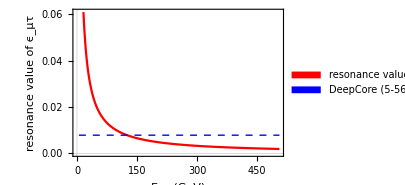

```mathematica
nres[En_]:=0.9895694989735606/En

Enrange={5,506}
Plot[nres[En],{En,Enrange[[1]],Enrange[[2]]},PlotRange->{0,0.061},PlotStyle->Red(*,Blue,Darker@Green*),FrameLabel->{"E_ν (GeV)","resonance value of ϵ_μτ"},PlotLegends->Placed[SwatchLegend[{Red,Blue,Darker@Green},{"resonance value","DeepCore (5-56 GeV)\n upper bound"}],{0.7,0.35}],PlotTheme->"Scientific",FrameStyle->Directive["Times",Black,16],Epilog->{Blue,Dashed,Line[{{Enrange[[1]],0.0079},{Enrange[[2]],0.0079}}]},Frame->True,ImageSize->300]
```

```mathematica
H0+HLIV
```

### Find resonance in H0+Hmatter+NSI

```mathematica
Clear[mix2,free2,free2v2,mat2,vals,vecs]
mix2={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};free2={{0,0},{0,dm21/(2En)}};
free2v2=mix2.free2.Transpose[mix2];
matter2={{√2 GF ne ,0},{0,0}};
mat2=free2v2+matter2+ReplaceAll[√2 GF np{{aee,aem},{aem,amm}},{aee->0,aem->x ,amm->0}];
{vals,vecs}=Eigensystem[mat2];
(*normvecs={};*)
normvecs=Normalize/@vecs;
ord=Ordering[vals];          
mix2new=Transpose[normvecs[[ord]]];
mix2new=Simplify[mix2new,Assumptions->{dm21^2>0,dm21>0,x>0,θ>0,En>0}];
```

```mathematica
Simplify[mix2new[[2,1]]/.{x->0,ne->0,np->0},{dm21>0,π/2>θ>0}]
```

sin(θ)

```mathematica
simp11=Simplify[Numerator[mix2new[[1,1]]](*/.{x->0,ne->0,np->0}*),{dm21>0,π/2>θ>0,x>0,ne>0,np>0}]
Simplify[Numerator[mix2new[[2,1]]](*/.{x->0,ne->0,np->0}*),{dm21>0,π/2>θ>0,x>0,ne>0,np>0}]
```

-√(dm21^2-4 √2 dm21 En GF ne cos(2 θ)+8 √2 dm21 En GF np x sin(2 θ)+8 En^2 GF^2 ne^2+32 En^2 GF^2 np^2 x^2)-dm21 cos(2 θ)+2 √2 En GF ne

2

```mathematica
solve11=Solve[simp11==0,x,Assumptions->{dm21>0,π/2>θ>0,ne>0,np>0}]//FullSimplify
x/.solve11/.{GF->1.16*10^-5 (*GeV^-2*),dm21->2.5*10^-3*10^-18,θ->45 Degree,np->numearthnucldensity,ne->numearthnucldensity}//StandardForm
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→-(dm21 sin(2 θ))/(4 √2 En GF np)},{x→-(dm21 sin(2 θ))/(4 √2 En GF np)}}

{-0.989569/En,-0.989569/En}

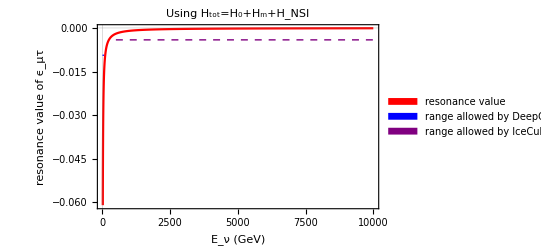

```mathematica
nresfullHam[En_]:=-0.9895694989735605/En

Enrange={5,10^4};
Plot[nresfullHam[En],{En,Enrange[[1]],Enrange[[2]]},(*ScalingFunctions->{"Log","Log"},*)PlotRange->{0.02,-0.061},PlotStyle->Red(*,Blue,Darker@Green*),FrameLabel->{"E_ν (GeV)","resonance value of ϵ_μτ"},PlotLegends->Placed[SwatchLegend[{Red,Blue,Purple},{"resonance value","range allowed by DeepCore\n(5-56 GeV) arXiv:2512.22632","range allowed by IceCube\n(0.5-10 TeV) arXiv:2201.03566"}],{0.7,0.35}],PlotTheme->"Scientific",FrameStyle->Directive["Times",Black,16],Epilog->{{Blue,Dashed,Line[{{5,0.0079},{56,0.0079}}],Line[{{5,-0.0094},{56,-0.0094}}]},{Purple,Dashed,Line[{{500,0.0031},{10^4,0.0031}}],Line[{{500,-0.0041},{10^4,-0.0041}}]}},PlotLabel->"Using H_tot=H_0+H_m+H_NSI",Frame->True,ImageSize->400]
```

### oscillation

```mathematica
mix2new//StandardForm
```

```mathematica
mix2newfunc[En_,GF_,ne_,np_,dm21_,θ_,x_]:={{(2 √2 En GF ne-dm21 Cos[2 θ]-√(dm21^2+8 En^2 GF^2 ne^2+32 En^2 GF^2 np^2 x^2-4 √2 dm21 En GF ne Cos[2 θ]+8 √2 dm21 En GF np x Sin[2 θ]))/(√(4+Abs[(-2 √2 En GF ne+dm21 Cos[2 θ]+√(dm21^2+8 En^2 GF^2 ne^2+32 En^2 GF^2 np^2 x^2-4 √2 dm21 En GF ne Cos[2 θ]+8 √2 dm21 En GF np x Sin[2 θ]))/(2 √2 En GF np x+dm21 Cos[θ] Sin[θ])]^2) (2 √2 En GF np x+dm21 Cos[θ] Sin[θ])),(2 √2 En GF ne-dm21 Cos[2 θ]+√(dm21^2+8 En^2 GF^2 ne^2+32 En^2 GF^2 np^2 x^2-4 √2 dm21 En GF ne Cos[2 θ]+8 √2 dm21 En GF np x Sin[2 θ]))/(√(1+Abs[(2 √2 En GF ne-dm21 Cos[2 θ]+√(dm21^2+8 En^2 GF^2 ne^2+32 En^2 GF^2 np^2 x^2-4 √2 dm21 En GF ne Cos[2 θ]+8 √2 dm21 En GF np x Sin[2 θ]))/(4 √2 En GF np x+dm21 Sin[2 θ])]^2) (4 √2 En GF np x+dm21 Sin[2 θ]))},{2/(√(4+Abs[(-2 √2 En GF ne+dm21 Cos[2 θ]+√(dm21^2+8 En^2 GF^2 ne^2+32 En^2 GF^2 np^2 x^2-4 √2 dm21 En GF ne Cos[2 θ]+8 √2 dm21 En GF np x Sin[2 θ]))/(2 √2 En GF np x+dm21 Cos[θ] Sin[θ])]^2)),1/(√(1+Abs[(2 √2 En GF ne-dm21 Cos[2 θ]+√(dm21^2+8 En^2 GF^2 ne^2+32 En^2 GF^2 np^2 x^2-4 √2 dm21 En GF ne Cos[2 θ]+8 √2 dm21 En GF np x Sin[2 θ]))/(4 √2 En GF np x+dm21 Sin[2 θ])]^2))}}
```

```mathematica
evol[10,1]//Simplify
```

```mathematica
evol[10000,0.3][[1,1]]
```

0.166734+0.471381 ⅈ

```mathematica
evol[L_,En_,α_,β_,x_]:=Module[{GF,ne,np,dm21,θ,makemix,tadaout,prob},
(*2x2 mixing matrix*)
makemix = mix2newfunc[En,GF,ne,np,dm21,θ,x]/.{GF->1.16*10^-5 (*GeV^-2*),dm21->2.5*10^-3,θ->45 Degree,np->numearthnucldensity,ne->numearthnucldensity};
(*Print[makemix];*)
(*tadaout=makemix.{{0,0},{0,Exp[-I 1.267(dm21 L)/En]}}.ConjugateTranspose[makemix]/.dm21->2.5*10^-3;*)
tadaout=makemix[[α,1]]Conjugate[makemix[[β,1]]]+makemix[[α,2]]Exp[-I 1.267(dm21 L)/En]Conjugate[makemix[[β,2]]]/.dm21->2.5*10^-3;
prob=tadaout Conjugate[tadaout];
prob

]
```

```mathematica
evol[100,1,1,2]
```

0.0248736+0. ⅈ

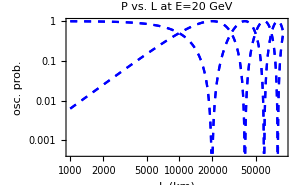

```mathematica
Plot[ {evol[L,20,1,1,0],evol[L,20,1,2,0],evol[L,20,1,1,1],evol[L,20,1,2,1]},{L,10^3,9 10^4},PlotRange->{0,1},ScalingFunctions->{"Log","Log"},PlotStyle->{{Directive[Red,Dotted],Directive[Blue,Dotted],Directive[Red,Dashed],Directive[Blue,Dashed]}},PlotLegends->Placed[LineLegend[{Directive[Red,Dotted],Directive[Blue,Dotted],Directive[Red,Dashed],Directive[Blue,Dashed]},{"P_μμ","P_μτ","P_μμ NSI","P_μτ NSI"}LegendFunction->"Frame",LegendMargins->2,LabelStyle->Directive["Times",Black,11]],{0.7,0.35}],FrameLabel->{"L (km)","osc. prob."},
PlotTheme->"Scientific",PlotLabel->"P vs. L at E=20 GeV",FrameStyle->Directive["Times",Black,16],Frame->True,ImageSize->300]
```

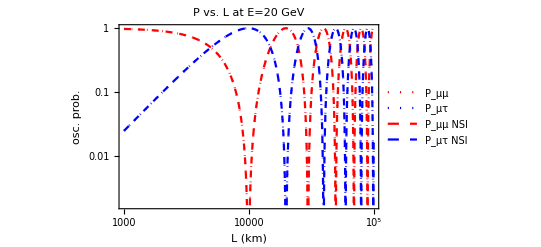

```mathematica
Plot[{evol[L,10,1,1,0],evol[L,10,1,2,0],evol[L,10,1,1,1],evol[L,10,1,2,1]},{L,10^3, 10^5},PlotRange->{0,1},PlotStyle->{Directive[Red,Dotted],Directive[Blue,Dotted],Directive[Red,Dashed],Directive[Blue,Dashed]},PlotLegends->Placed[LineLegend[{Directive[Red,Dotted],Directive[Blue,Dotted],Directive[Red,Dashed],Directive[Blue,Dashed]},{"P_μμ","P_μτ","P_μμ NSI","P_μτ NSI"},(*LegendFunction->"Frame",*)LegendMargins->2,LabelStyle->Directive["Times",Black,11]],{0.25,0.35}],(* <--adjust these coords to move legend inside*)ScalingFunctions->{"Log","Log"},FrameLabel->{"L (km)","osc. prob."},PlotTheme->"Scientific",PlotLabel->"P vs. L at E=20 GeV",FrameStyle->Directive["Times",Black,16],Frame->True,ImageSize->400]
```